```mathematica
Needs["MolecularCogs`","molecularCogsPackage.m"];
Needs["AffinityPropagation3`","affinityPropagationPackage3.m"];
Needs["SpectralClustering`","spectralClusteringPackage.m"];

Needs["ErrorBarPlots`"]
```

PREFIX::shdw: Symbol "PREFIX" appears in multiple contexts {"AffinityPropagation3`", "Global`"}; definitions in context "AffinityPropagation3`" may shadow or be shadowed by other definitions.

i::shdw: Symbol "i" appears in multiple contexts {"AffinityPropagation3`", "Global`"}; definitions in context "AffinityPropagation3`" may shadow or be shadowed by other definitions.

tmp::shdw: Symbol "tmp" appears in multiple contexts {"AffinityPropagation3`", "Global`"}; definitions in context "AffinityPropagation3`" may shadow or be shadowed by other definitions.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{"whichAtomsForDih    1", 5, 6, 7}].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{"whichAtomsForAux    2", 1, 5, "6     # atom numbers forming the auxiliary dihedral angle"}].

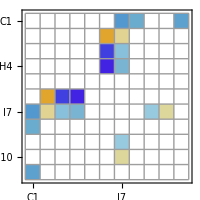

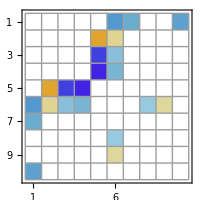

```mathematica
howToSetTheDiagonal=3;
interaction="ele";
textSize=16;
mats=reapForOneAngle["-134.50","Mean"];
mat=mats⟦interactionPosition[interaction]⟧;
myMatrixPlot[mat,Range[Length[mat]],textSize,200]
{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,50,50];

simMats={packedMat,-packedMat};
MatrixPlot[packedMat,Mesh->True]
```

```mathematica
textSize=14;
imageSize=2.9;
```

vdw

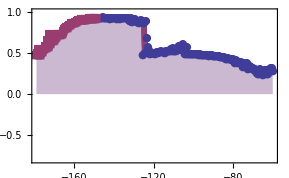

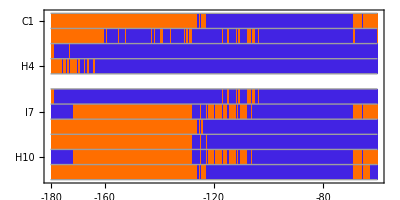
-Graphics-ξ [degrees]

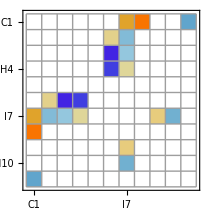

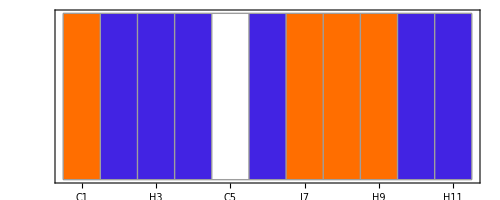
-Graphics-SCORE = 0.968

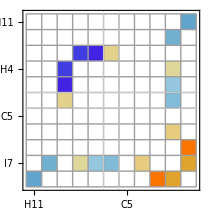

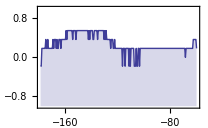

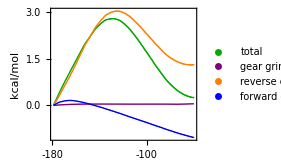

```mathematica
{p1,p2,p3,p4,p5,p6,p8}=plotListPlotAndStripe["vdw","vdw",textSize,72*imageSize];
```

Reading wyniki_ele_ii-nh3.str

ele

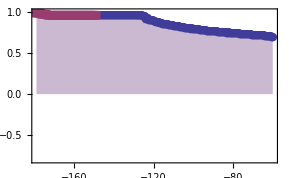

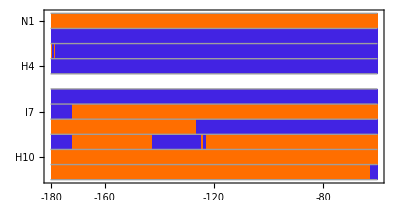
-Graphics-ξ [degrees]

ele

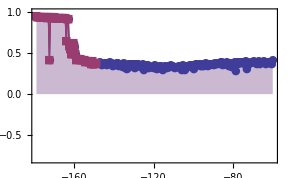

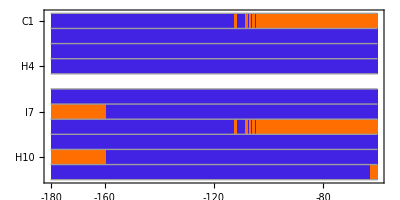
-Graphics-ξ [degrees]

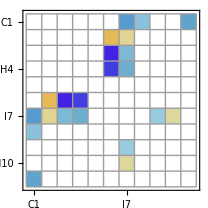

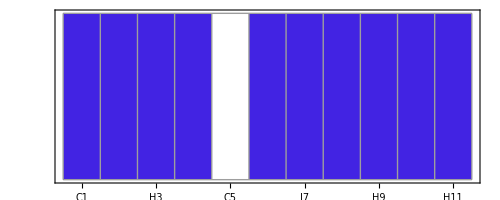
-Graphics-SCORE = 0.381

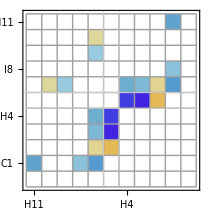

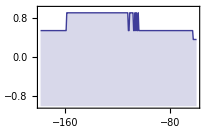

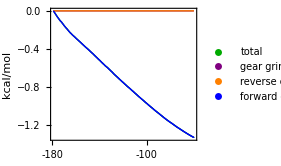

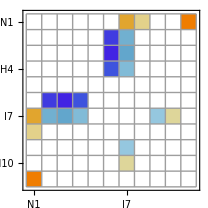

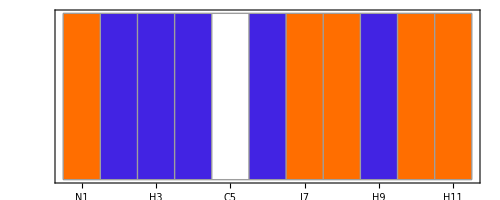
-Graphics-SCORE = 0.980

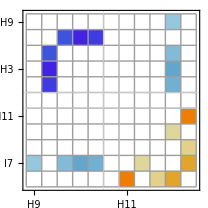

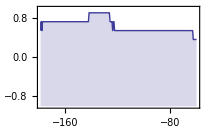

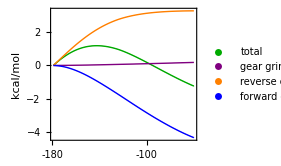

```mathematica
{p1,p2,p3,p4,p5,p6,p8}=plotListPlotAndStripe["ele","ele",textSize,72*imageSize];
```

non-bonded

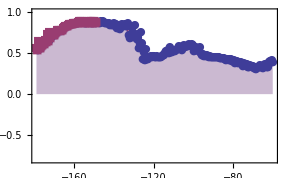

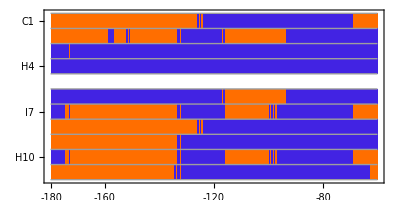
-Graphics-ξ [degrees]

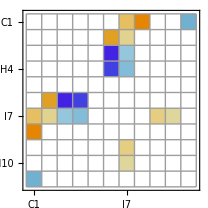

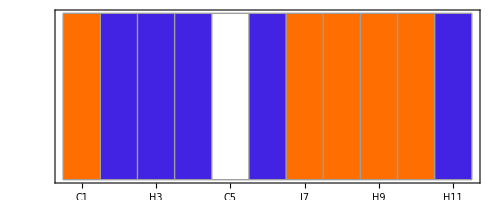
-Graphics-SCORE = 0.748

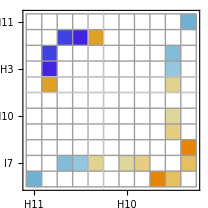

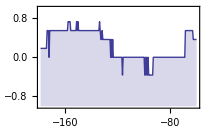

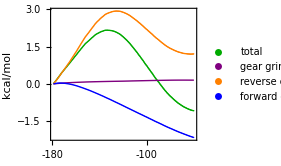

```mathematica
{p1,p2,p3,p4,p5,p6,p8}=plotListPlotAndStripe["non-bonded","nbd",textSize,72*imageSize];
```

bonds

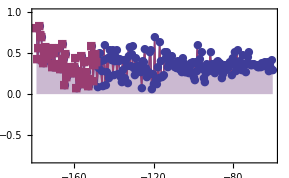

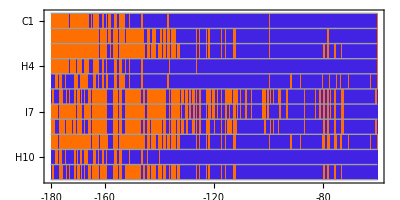
-Graphics-ξ [degrees]

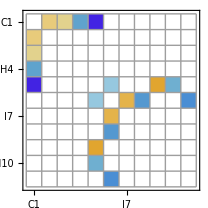

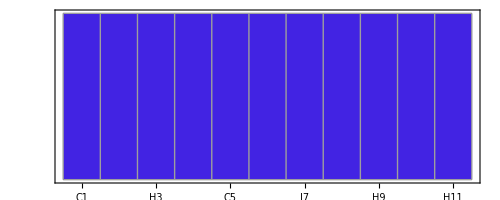
-Graphics-SCORE = 0.187

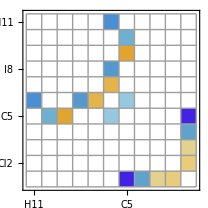

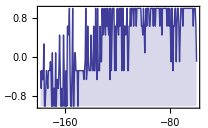

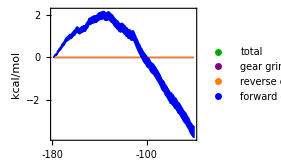

```mathematica
{p1,p2,p3,p4,p5,p6,p8}=plotListPlotAndStripe["bonds","bond",textSize,72*imageSize];
```

Reading wyniki_conf_ii-ccl.str

conf

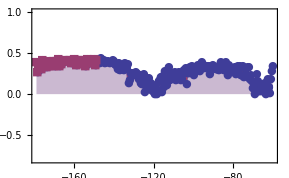

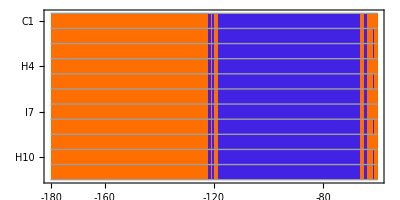
-Graphics-ξ [degrees]

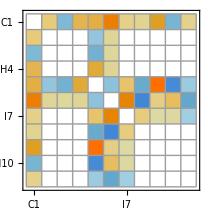

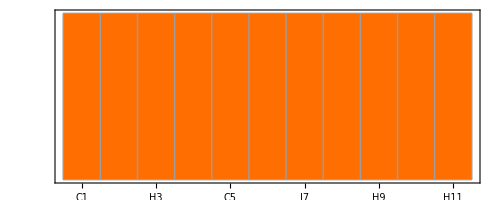
-Graphics-SCORE = 0.178

-Graphics-

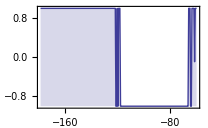

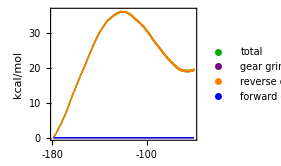

tors

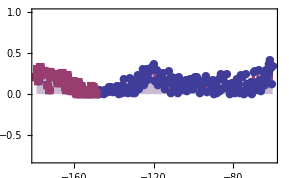

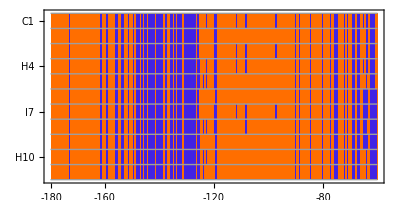
-Graphics-ξ [degrees]

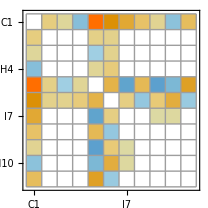

-Graphics-SCORE = 0.307

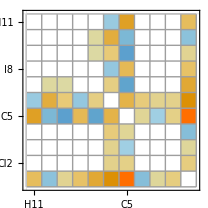

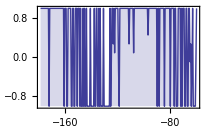

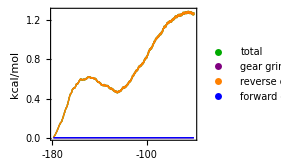

```mathematica
{p1,p2,p3,p4,p5,p6,p8}=plotListPlotAndStripe["conf","conf",textSize,72*imageSize];

(*{p1,p2,p3,p4,p5,p6,p8}=plotListPlotAndStripe["angle","angl",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p8}=plotListPlotAndStripe["tors","tors",textSize,72*imageSize];
;*)
```

all

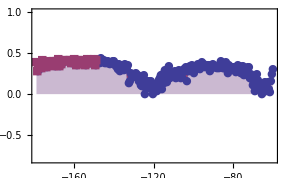

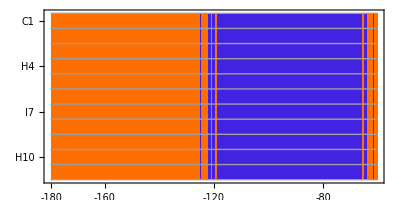
-Graphics-ξ [degrees]

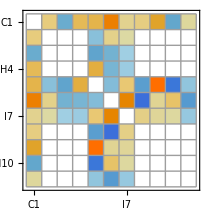

-Graphics-SCORE = 0.157

-Graphics-

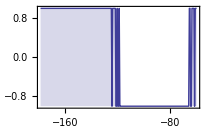

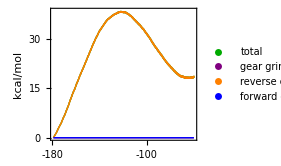

```mathematica
{p1,p2,p3,p4,p5,p6,p8}=plotListPlotAndStripe["all","total",textSize,72*imageSize];
```